```mathematica
Klm0:=Import["/home/isabel/Desktop/Physik/CLASS/class/prelim/Km_000.dat","Data"]
```

```mathematica
Klm1:=Import["/home/isabel/Desktop/Physik/CLASS/class/prelim/Km_001.dat","Data"]
```

```mathematica
Klm2:=Import["/home/isabel/Desktop/Physik/CLASS/class/prelim/Km_002.dat","Data"]
```

```mathematica
Klm3:=Import["/home/isabel/Desktop/Physik/CLASS/class/prelim/Km_003.dat","Data"]
```

```mathematica
Klm3[[1]]
```

{0.0317166,0.000547065,0.000415098,0.000394953,0.000409272,0.000437334,0.000472079,0.00051053,0.000551236,0.00059341}

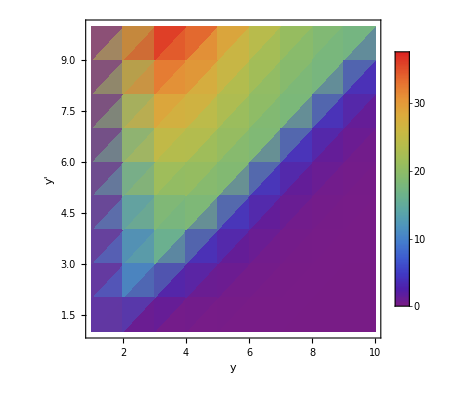

```mathematica
ListDensityPlot[ 1/(0.71611)^4Transpose[Klm0[[1;;10,1;;10]]] ,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->12,Black}],FrameLabel->{Style[y,FontFamily->"Lato", FontSize->18, Black],Style[y',FontFamily->"Lato", FontSize->18,Black]},ColorFunction->"Rainbow",FrameTicksStyle->Directive[Black,12],PlotRange->All]
```

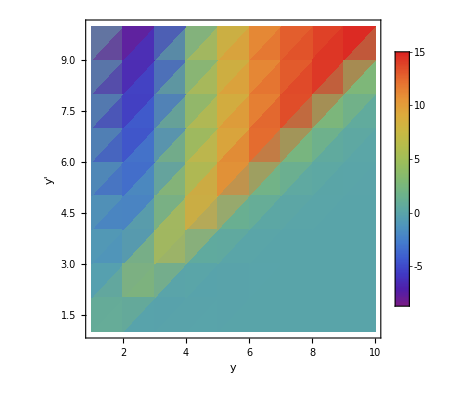

```mathematica
ListDensityPlot[1/(0.71611)^4Transpose[Klm1[[1;;10,1;;10]]] ,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->12,Black}],FrameLabel->{Style[y,FontFamily->"Lato", FontSize->18, Black],Style[y',FontFamily->"Lato", FontSize->18,Black]},ColorFunction->"Rainbow",FrameTicksStyle->Directive[Black,12],PlotRange->All]
```

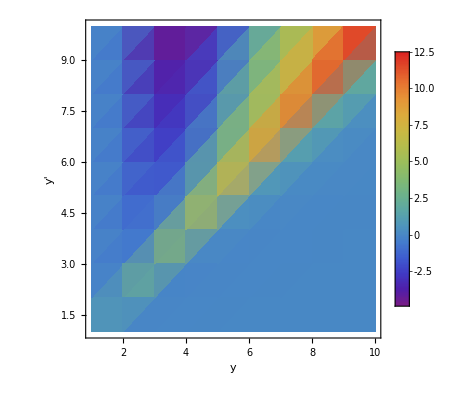

```mathematica
ListDensityPlot[1/(0.71611)^4Transpose[Klm2[[1;;10,1;;10]]] ,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->12,Black}],FrameLabel->{Style[y,FontFamily->"Lato", FontSize->18, Black],Style[y',FontFamily->"Lato", FontSize->18,Black]},ColorFunction->"Rainbow",FrameTicksStyle->Directive[Black,12],PlotRange->All]
```

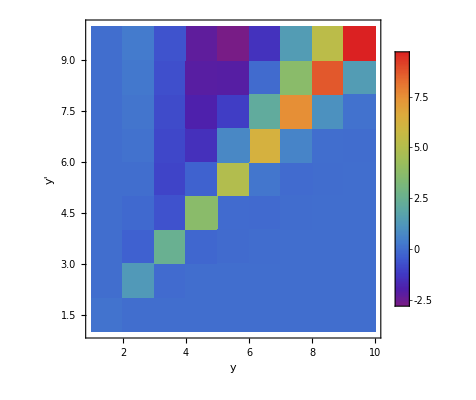

```mathematica
ListDensityPlot[1/(0.71611)^4Transpose[Klm3[[1;;10,1;;10]]] ,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->12,Black}],FrameLabel->{Style[y,FontFamily->"Lato", FontSize->18, Black],Style[y',FontFamily->"Lato", FontSize->18,Black]},ColorFunction->"Rainbow",FrameTicksStyle->Directive[Black,12],PlotRange->All,InterpolationOrder->0]
```

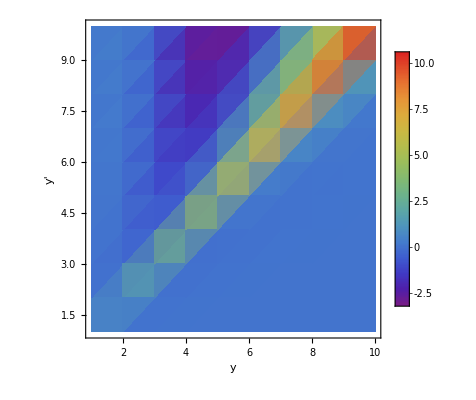

```mathematica
ListDensityPlot[1/(0.71611)^4Transpose[Klm3[[1;;10,1;;10]]] ,PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->12,Black}],FrameLabel->{Style[y,FontFamily->"Lato", FontSize->18, Black],Style[y',FontFamily->"Lato", FontSize->18,Black]},ColorFunction->"Rainbow",FrameTicksStyle->Directive[Black,12],PlotRange->All]
```